```mathematica
f[x_]:=x^3+Sin[x]-12x+1
```

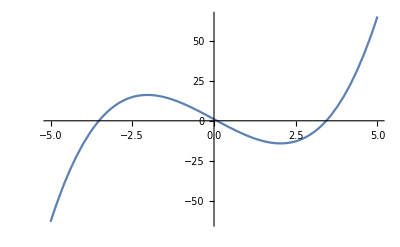

```mathematica
Plot[f[x],{x,-5,5}]
```

```mathematica
ϵ=1/2*10^-4
```

1/20000

Нулевое приближение для отрицательного корня

```mathematica
x01=-3.5
ϕ1[x_]:=x-f[x]/f'[x01]
```

-3.5

Графическая проверка теоремы

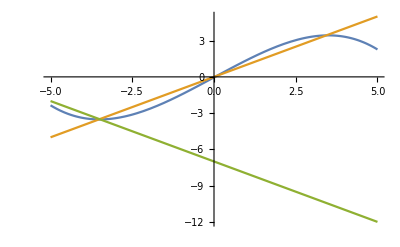

```mathematica
Plot[{ϕ1[x],x,-(x+3.5)-3.5},{x,-5,5}]
```

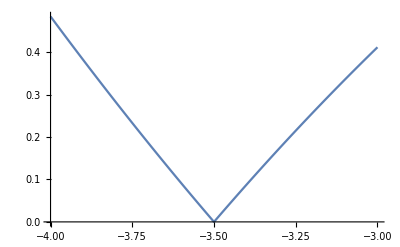

1/2

```mathematica
Plot[Abs[ϕ1'[x]],{x,-4,-3}]
q1=1/2
```

```mathematica
Abs[x01-ϕ1[x01]]
m1=0.02
```

0.0199795

0.02

```mathematica
m1/(1-q1)<Abs[(-4+3)]/2
```

True

```mathematica
x1n={}
AppendTo[x1n,x01]
AppendTo[x1n,ϕ1[x01]]
```

{}

{-3.5}

{-3.5,-3.51998}

```mathematica
For[i=2,Abs[x1n⟦i-1⟧-x1n⟦i⟧]>ϵ,i++,AppendTo[x1n,ϕ1[x1n⟦i⟧]]]
```

List

```mathematica
x1n
```

{-3.5,-3.51998,-3.5198,-3.5198}

```mathematica
f[x1n⟦4⟧]
```

-1.36083×10^-6

Нулевое приближение для первого положительного корня

```mathematica
x02=0.25
ϕ2[x_]:=x-f[x]/f'[x02]
```

0.25

Графическая проверка теоремы

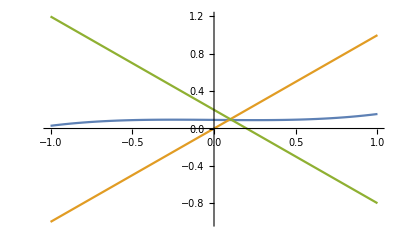

```mathematica
Plot[{ϕ2[x],x,-(x-0.1)+0.1},{x,-1,1}]
```

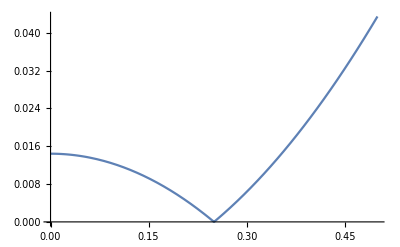

0.0434515

```mathematica
Plot[Abs[ϕ2'[x]],{x,0,1/2}]
q2=Abs[ϕ2'[1/2]]
```

```mathematica
Abs[x02-ϕ2[x02]]//N
m2=Abs[x02-ϕ2[x02]]
```

0.160184

0.160184

```mathematica
m2/(1-q2)<1/4
```

True

```mathematica
x2n={}
AppendTo[x2n,x02]
AppendTo[x2n,ϕ2[x02]]
```

{}

{0.25}

{0.25,0.0898158}

```mathematica
For[i=2,Abs[x2n⟦i-1⟧-x2n⟦i⟧]>ϵ,i++,AppendTo[x2n,ϕ2[x2n⟦i⟧]]]
```

```mathematica
x2n
```

{0.25,0.0898158,0.0909805,0.0909659}

```mathematica
f[x2n⟦-1⟧]
```

1.98226×10^-6

Нулевое приближение для второго положительного корня

```mathematica
x03=3.5
ϕ3[x_]:=x-f[x]/f'[x03]
```

3.5

Графическая проверка теоремы

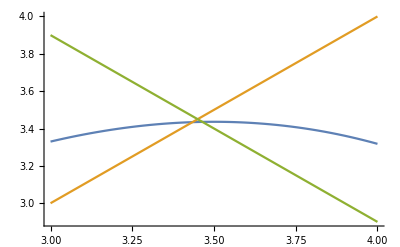

```mathematica
Plot[{ϕ3[x],x,-(x-3.5)+3.4},{x,3,4}]
```

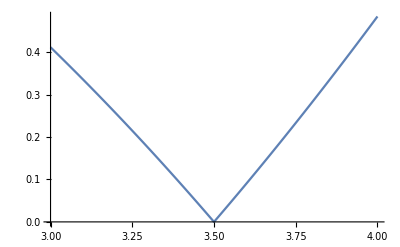

0.484296

```mathematica
Plot[Abs[ϕ3'[x]],{x,3,4}]
q3=Abs[ϕ3'[4]]
```

```mathematica
Abs[x03-ϕ3[x03]]//N
m3=Abs[x03-ϕ3[x03]]
```

0.0640063

0.0640063

```mathematica
m3/(1-q3)<1/2
```

True

```mathematica
x3n={}
AppendTo[x3n,x03]
AppendTo[x3n,ϕ2[x03]]
```

{}

{3.5}

{3.5,3.64056}

```mathematica
For[i=2,Abs[x3n⟦i-1⟧-x3n⟦i⟧]>ϵ,i++,AppendTo[x3n,ϕ3[x3n⟦i⟧]]]
```

```mathematica
x3n
```

{3.5,3.64056,3.427,3.43362,3.43403,3.43406}

```mathematica
f[x3n⟦-1⟧]
```

-0.0000334446